```mathematica
SetDirectory["D:\\program files\\Wolfram Research\\Mathematica\\7.0\\AddOns\\ExtraPackages\\MadEvent analysis\\parameter_scans\\plots_for_pub"];
Timing[testp=Import["ax_decay.lhe","Table"];]
```

{7.76885,Null}

```mathematica
Timing[testp2=Import["grv_decay.lhe","Table"];]
```

{9.20406,Null}

```mathematica
Timing[testp3=Import["rpv_decay.lhe","Table"];]
```

{7.95605,Null}

```mathematica
Timing[eventListp=ReadME[testp]; ]
```

{0.1716,Null}

```mathematica
Timing[eventListp2=ReadME[testp2]; ]
```

{0.2184,Null}

```mathematica
Timing[eventListp3=ReadME[testp3]; ]
```

{0.1716,Null}

```mathematica
Nev = 10000
```

10000

```mathematica
Nev2 = 10000
```

10000

```mathematica
Nev3 = Length[eventListp3]
```

10001

```mathematica
tsp={eventListp[[2]],eventListp2[[3]]};


EventPrint /@ %;
```

(pid | in/out | mother1 | mother2 | color1 | color2 | px | py | pz | p0 | mass | 6 | hel
c | finout[0] | 1.0737×10^-20 | 200. | 0.00781653 | 0.10537 | 0 | 0 | 0 | 0 | 0 | 0 | 0
(χ̃)_0 | in | 0 | 0 | 0 | 0 | 0. | 0. | 1.×10^-14 | 202.304 | 202.304 | 0. | 1.
particle[9000006] | out | 1 | 0 | 0 | 0 | 48.8704 | 25.0771 | -40.1198 | 68.0204 | 0. | 0. | -1.
u | out | 1 | 0 | 501 | 0 | -36.763 | 39.0672 | 43.285 | 68.9301 | 0. | 0. | 1.
uBar | out | 1 | 0 | 0 | 501 | -12.1074 | -64.1443 | -3.16524 | 65.3537 | 0. | 0. | -1.)

(pid | in/out | mother1 | mother2 | color1 | color2 | px | py | pz | p0 | mass | 6 | hel
c | finout[0] | 9.3538×10^-21 | 200. | 0.00781653 | 0.10537 | 0 | 0 | 0 | 0 | 0 | 0 | 0
(χ̃)_0 | in | 0 | 0 | 0 | 0 | 0. | 0. | 1.×10^-14 | 202.304 | 202.304 | 0. | -1.
particle[1000049] | out | 1 | 0 | 0 | 0 | -45.5333 | -80.2961 | 40.4314 | 100.774 | 5.×10^-7 | 0. | 1.
u | out | 1 | 0 | 501 | 0 | 10.5714 | 10.0269 | -4.86423 | 15.3608 | 0. | 0. | -1.
uBar | out | 1 | 0 | 0 | 501 | 34.9619 | 70.2693 | -35.5671 | 86.1692 | 0. | 0. | 1.
particle[0] | finout[0] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
eventListOutLp=SetOut[eventListp];
```

```mathematica
eventListOutLp2=SetOut[eventListp2];
eventListOutLp3=SetOut[eventListp3];
```

```mathematica
{eventListOutLp3[[3]],eventListOutLp[[24]]};
EventPrint /@ %;
```

(pid | in/out | mother1 | mother2 | color1 | color2 | px | py | pz | p0 | mass | 6 | hel
c | finout[0] | 1.0363×10^-20 | 200. | 0.00781653 | 0.10537 | 0 | 0 | 0 | 0 | 0 | 0 | 0
(⋁_e)^c | out | 1 | 0 | 0 | 0 | -32.6195 | -6.29595 | 67.5773 | 75.3018 | 0. | 0. | 1.
d | out | 1 | 0 | 501 | 0 | 56.3091 | 1.64244 | -81.5447 | 99.1108 | 0. | 0. | 1.
dBar | out | 1 | 0 | 0 | 501 | -23.6896 | 4.65351 | 13.9674 | 27.8916 | 0. | 0. | 1.)

(pid | in/out | mother1 | mother2 | color1 | color2 | px | py | pz | p0 | mass | 6 | hel
c | finout[0] | 1.0737×10^-20 | 200. | 0.00781653 | 0.10537 | 0 | 0 | 0 | 0 | 0 | 0 | 0
particle[9000006] | out | 1 | 0 | 0 | 0 | 54.3208 | -24.9423 | -48.8052 | 77.1675 | 0. | 0. | 1.
c | out | 1 | 0 | 501 | 0 | -9.75513 | 37.7343 | 65.1976 | 75.959 | 0. | 0. | 1.
cBar | out | 1 | 0 | 0 | 501 | -44.5657 | -12.792 | -16.3924 | 49.1777 | 0. | 0. | -1.)

```mathematica
weight[event_]:=weightOf[event[[1]]];
ptmiss[event_]:=ptOf[event[[2]]];
missingEnergy[event_]:=enOf[event[[2]]];
MHT[event_]:=Abs[√((-pxOf[event[[3]]]- pxOf[event[[4]]])^2+(-pyOf[event[[3]]]-pyOf[event[[4]]])^2)];
energy2[event_]:=enOf[event[[3]]];
energy3[event_]:=enOf[event[[4]]];
JetInvMass[event_] := Sqrt[2*(enOf[event[[3]]]*enOf[event[[4]]]-ThreeVectorFrom[event[[3]]].ThreeVectorFrom[event[[4]]])];
ptJettot[event_]:=ptOf[event[[3]]]+ptOf[event[[4]]];
ptHardest[event_]:=Which[ptOf[event[[3]]]>ptOf[event[[4]]],ptOf[event[[3]]],ptOf[event[[4]]]>ptOf[event[[3]]],ptOf[event[[4]]]];
ptSoftest[event_]:=Which[ptOf[event[[3]]]<ptOf[event[[4]]],ptOf[event[[3]]],ptOf[event[[4]]]<ptOf[event[[3]]],ptOf[event[[4]]]];
etaHardest[event_]:=Which[ptOf[event[[3]]]>ptOf[event[[4]]],etaOf[event[[3]]],ptOf[event[[4]]]>ptOf[event[[3]]],ptOf[event[[4]]]];
thetaHardest[event_]:=Which[ptOf[event[[3]]]>ptOf[event[[4]]],thetaOf[event[[3]]],ptOf[event[[4]]]>ptOf[event[[3]]],ptOf[event[[4]]]];
phiHardest[event_]:=Which[ptOf[event[[3]]]>ptOf[event[[4]]]&,phiOf[event[[3]]],ptOf[event[[4]]]>ptOf[event[[3]]],phiOf[event[[4]]],];
etaSoftest[event_]:=Which[ptOf[event[[3]]]<ptOf[event[[4]]],etaOf[event[[3]]],ptOf[event[[4]]]<ptOf[event[[3]]],etaOf[event[[4]]]];
thetaSoftest[event_]:=Which[ptOf[event[[3]]]<ptOf[event[[4]]],thetaOf[event[[3]]],ptOf[event[[4]]]<ptOf[event[[3]]],thetaOf[event[[4]]]];
phiSoftest[event_]:=Which[ptOf[event[[3]]]<ptOf[event[[4]]],phiOf[event[[3]]],ptOf[event[[4]]]<ptOf[event[[3]]],phiOf[event[[4]]],];
drjj[event_]:=√((etaOf[event[[3]]]-etaOf[event[[4]]])^2-(phiOf[event[[3]]]-phiOf[event[[4]]])^2);


ptJettotAxPlot = Map[ptJettot[#] &, eventListOutLp[[1;;Nev]]];
ptJettotGrvPlot = Map[ptJettot[#] &, eventListOutLp2[[1;;Nev2]]];
ptJettotRPVPlot= Map[ptJettot[#] &, eventListOutLp3[[1;;Nev3]]];

weightListAx=Map[5.4/(1.11*10^-16)*weight[#]&,eventListOutLp[[1;;Nev]]];
weightListGrv=Map[5.4/(1.066*10^-15)*(0.9*10^-20)&,eventListOutLp2[[1;;Nev2]]];
weightListRPV=Map[5.4/(2.275*10^-16)*weight[#]&,eventListOutLp3[[1;;Nev3]]];

ptHardestAxPlot = Map[ptHardest[#] &, eventListOutLp[[1;;Nev]]];
ptHardestGrvPlot = Map[ptHardest[#] &, eventListOutLp2[[1;;Nev2]]];
ptHardestRPVPlot = Map[ptHardest[#] &, eventListOutLp3[[1;;Nev3]]];

ptSoftestAxPlot = Map[ptSoftest[#] &, eventListOutLp[[1;;Nev]]];
ptSoftestGrvPlot = Map[ptSoftest[#] &, eventListOutLp2[[1;;Nev2]]];
ptSoftestRPVPlot = Map[ptSoftest[#] &, eventListOutLp3[[1;;Nev3]]];

ptmissAxPlot = Map[ptmiss[#] &, eventListOutLp[[1;;Nev]]];
ptmissGrvPlot = Map[ptmiss[#] &, eventListOutLp2[[1;;Nev2]]];
ptmissRPVPlot = Map[ptmiss[#] &, eventListOutLp3[[1;;Nev3]]];

missingEnergyAxPlot = Map[missingEnergy[#] &, eventListOutLp[[1;;Nev]]];
missingEnergyGrvPlot = Map[missingEnergy[#] &, eventListOutLp2[[1;;Nev2]]];
missingEnergyRPVPlot = Map[missingEnergy[#] &, eventListOutLp3[[1;;Nev3]]];

JetInvMassAxPlot = Map[JetInvMass[#] &, eventListOutLp[[1;;Nev]]];
JetInvMassGrvPlot = Map[JetInvMass[#] &, eventListOutLp2[[1;;Nev2]]];
JetInvMassRPVPlot = Map[JetInvMass[#] &, eventListOutLp3[[1;;Nev3]]];

ptSoftestAxPlot= Map[ptSoftest[#] &, eventListOutLp[[1;;Nev]]];
ptSoftestGrvPlot= Map[ptSoftest[#] &, eventListOutLp2[[1;;Nev2]]];
ptSoftestRPVPlot= Map[ptSoftest[#] &, eventListOutLp3[[1;;Nev3]]];


etaHardestAxPlot=Map[etaHardest[#] &, eventListOutLp[[1;;Nev]]];
etaHardestGrvPlot=Map[etaHardest[#] &, eventListOutLp2[[1;;Nev2]]];
etaHardestRPVPlot=Map[etaHardest[#] &, eventListOutLp3[[1;;Nev3]]];

thetaHardestAxPlot=Map[thetaHardest[#] &, eventListOutLp[[1;;Nev]]];
{{thetaHardestGrvPlot=Map[thetaHardest[#] &, eventListOutLp2[[1;;Nev2]]];}, {thetaHardestRPVPlot=Map[thetaHardest[#] &, eventListOutLp3[[1;;Nev3]]];}}

etaSoftestAxPlot=Map[etaSoftest[#] &, eventListOutLp[[1;;Nev]]];
etaSoftestGrvPlot=Map[etaSoftest[#] &, eventListOutLp2[[1;;Nev2]]];
etaSoftestRPVPlot=Map[etaSoftest[#] &, eventListOutLp3[[1;;Nev3]]];

thetaSoftestAxPlot=Map[thetaSoftest[#] &, eventListOutLp[[1;;Nev]]];
thetaSoftestGrvPlot=Map[thetaSoftest[#] &, eventListOutLp2[[1;;Nev2]]];
thetaSoftestRPVPlot=Map[thetaSoftest[#] &, eventListOutLp3[[1;;Nev3]]];

drjjAxPlot = Map[drjj[#] &, eventListOutLp[[1;;Nev]]];
drjjGrvPlot = Map[drjj[#] &, eventListOutLp2[[1;;Nev2]]];
drjjRPVPlot = Map[drjj[#] &, eventListOutLp3[[1;;Nev3]]];


energy2AxPlot = Map[energy2[#] &, eventListOutLp[[1;;Nev]]];
energy2GrvPlot = Map[energy2[#] &, eventListOutLp2[[1;;Nev2]]];
energy2RPVPlot = Map[energy2[#] &, eventListOutLp3[[1;;Nev3]]];

energy3AxPlot = Map[energy3[#] &, eventListOutLp[[1;;Nev]]];
energy3GrvPlot = Map[energy3[#] &, eventListOutLp2[[1;;Nev2]]];
energy3RPVPlot = Map[energy3[#] &, eventListOutLp3[[1;;Nev3]]];

MHTAxPlot = Map[MHT[#] &, eventListOutLp[[1;;Nev]]];
MHTGrvPlot = Map[MHT[#] &, eventListOutLp2[[1;;Nev2]]];
MHTRPVPlot = Map[MHT[#] &, eventListOutLp3[[1;;Nev3]]];
```

{{Null},{Null}}

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0\ ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0\ ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0\ ComplexInfinity encountered.

General::stop: Further output of Infinity :: indet will be suppressed during this calculation.

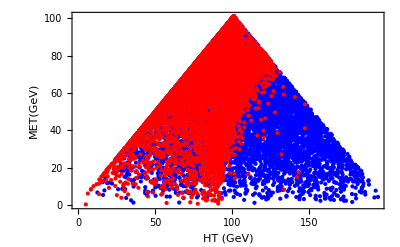

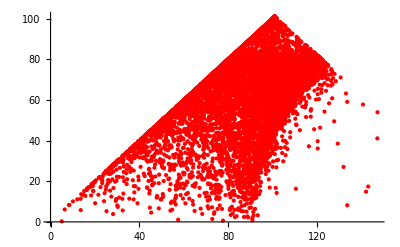

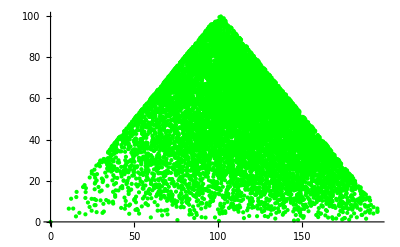

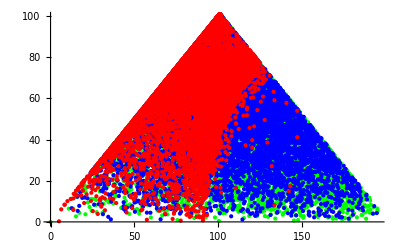

```mathematica
HtvsMETAxdata=Transpose@{ptJettotAxPlot,ptmissAxPlot};
HtvsMETGrvdata=Transpose@{ptJettotGrvPlot,ptmissGrvPlot};
HtvsMETRPVdata=Transpose@{ptJettotRPVPlot,ptmissRPVPlot};
SetOptions[ListPlot,BaseStyle->{FontFamily->"Times",FontSize->20}];
g1=ListPlot[{HtvsMETAxdata,HtvsMETGrvdata},PlotStyle->{Blue,Red},ImageSize->Scaled[.4],Frame->True,FrameLabel->{"HT (GeV)","MET(GeV)"}]
g2=ListPlot[HtvsMETGrvdata,PlotStyle->Red]
g3 =ListPlot[HtvsMETRPVdata,PlotStyle->Green]
Show[g3,g1]
```

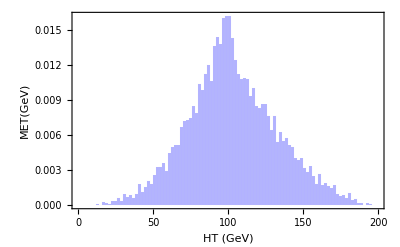

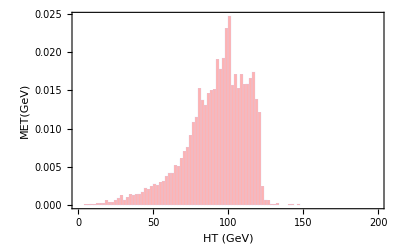

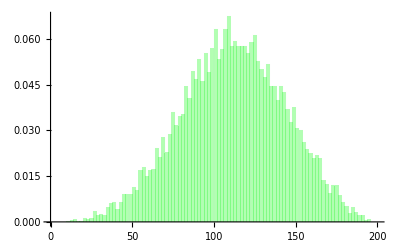

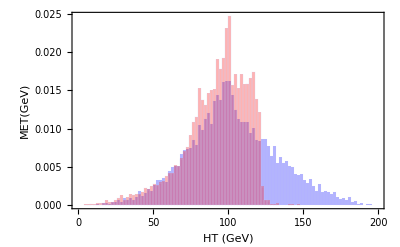

```mathematica
g1=WeightedHistogram[weightListGrv->ptJettotAxPlot, {0,200,2},ChartStyle->{Directive[Blue,Opacity[.3]]},BaseStyle->{FontWeight->"Bold",FontSize->18},Axes->True,AxesOrigin->{0,0},ImageSize->Scaled[.4],Frame->True,FrameLabel->{"HT (GeV)","# Events"}]
g2=WeightedHistogram[weightListGrv->ptJettotGrvPlot, {0,200,2},ChartStyle->{Directive[Red,Opacity[.3]]},BaseStyle->{FontWeight->"Bold",FontSize->18},Axes->True,AxesOrigin->{0,0},ImageSize->Scaled[.4],Frame->True,FrameLabel->{"HT (GeV)","MET(GeV)"}]
g3=WeightedHistogram[weightListRPV->ptJettotRPVPlot, {0,200,2},ChartStyle->{Directive[Green,Opacity[.3]]},BaseStyle->{FontWeight->"Bold",FontSize->18},Axes->True,AxesOrigin->{0,0}]

Show[g1,g2]
```

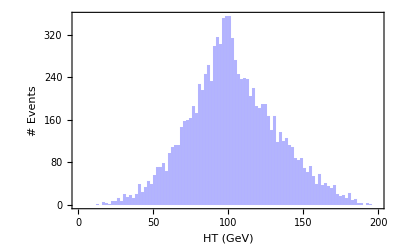

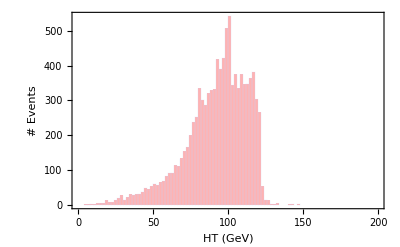

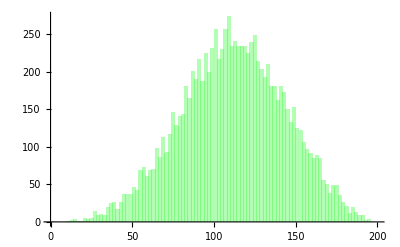

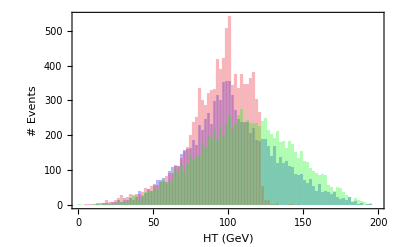

```mathematica
g1=Histogram[ptJettotAxPlot, {0,200,2},ChartStyle->{Directive[Blue,Opacity[.3]]},BaseStyle->{FontWeight->"Bold",FontSize->18},Axes->True,AxesOrigin->{0,0},ImageSize->Scaled[.4],Frame->True,FrameLabel->{"HT (GeV)","# Events"}]
g2=Histogram[ptJettotGrvPlot, {0,200,2},ChartStyle->{Directive[Red,Opacity[.3]]},BaseStyle->{FontWeight->"Bold",FontSize->18},Axes->True,AxesOrigin->{0,0},ImageSize->Scaled[.4],Frame->True,FrameLabel->{"HT (GeV)","# Events"}]
g3=Histogram[ptJettotRPVPlot, {0,200,2},ChartStyle->{Directive[Green,Opacity[.3]]},BaseStyle->{FontWeight->"Bold",FontSize->18},Axes->True,AxesOrigin->{0,0}]
Show[g1,g2,g3]
```

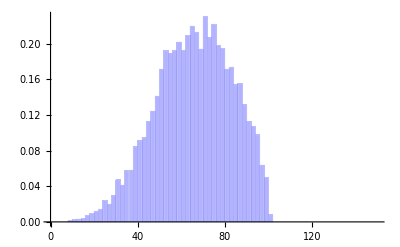

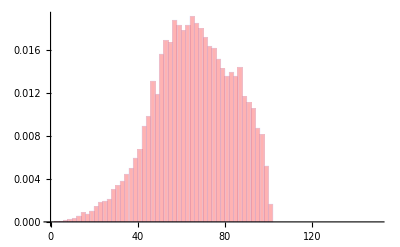

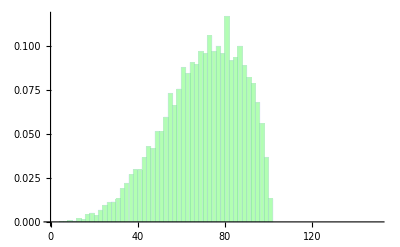

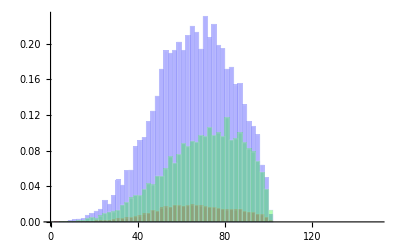

```mathematica
g1=WeightedHistogram[weightListAx->ptHardestAxPlot, {0,150,2},ChartStyle->{Directive[Blue,Opacity[.3]]},BaseStyle->{FontWeight->"Bold",FontSize->18},Axes->True,AxesOrigin->{0,0}]
g2=WeightedHistogram[weightListGrv->ptHardestGrvPlot,{0,150,2},ChartStyle->{Directive[Red,Opacity[.3]]},BaseStyle->{FontWeight->"Bold",FontSize->18},Axes->True,AxesOrigin->{0,0}]
g3=WeightedHistogram[weightListRPV->ptHardestRPVPlot,{0,150,2},ChartStyle->{Directive[Green,Opacity[.3]]},BaseStyle->{FontWeight->"Bold",FontSize->18},Axes->True,AxesOrigin->{0,0}]

Show[g1,g2,g3]
```

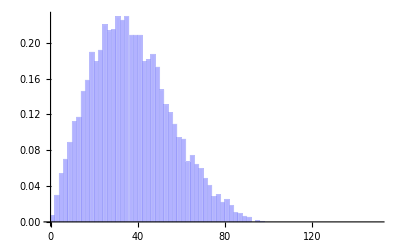

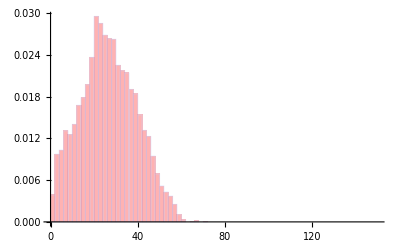

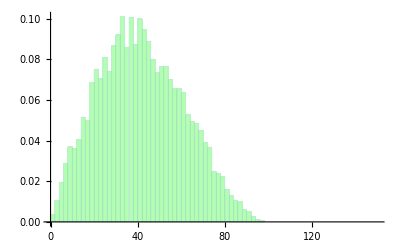

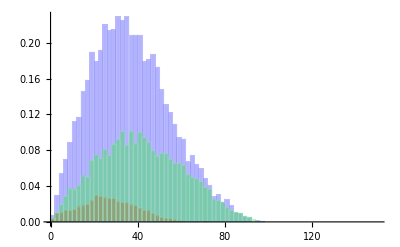

```mathematica
g1=WeightedHistogram[weightListAx->ptSoftestAxPlot, {0,150,2},ChartStyle->{Directive[Blue,Opacity[.3]]},BaseStyle->{FontWeight->"Bold",FontSize->18},Axes->True,AxesOrigin->{0,0}]
g2=WeightedHistogram[weightListGrv->ptSoftestGrvPlot,{0,150,2},ChartStyle->{Directive[Red,Opacity[.3]]},BaseStyle->{FontWeight->"Bold",FontSize->18},Axes->True,AxesOrigin->{0,0}]
g3=WeightedHistogram[weightListRPV->ptSoftestRPVPlot,{0,150,2},ChartStyle->{Directive[Green,Opacity[.3]]},BaseStyle->{FontWeight->"Bold",FontSize->18},Axes->True,AxesOrigin->{0,0}]
Show[g1,g2,g3]
```

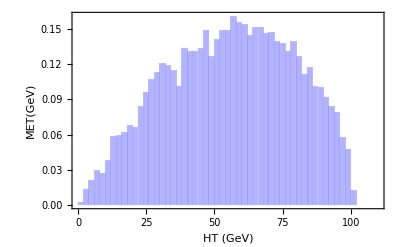

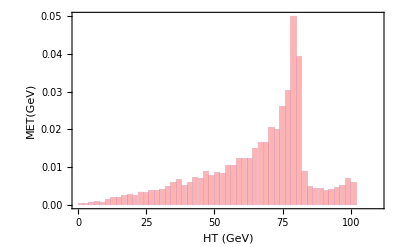

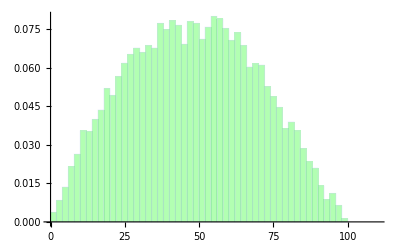

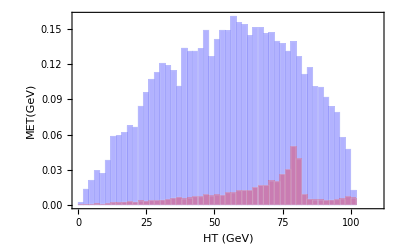

```mathematica
g1=WeightedHistogram[weightListAx->ptmissAxPlot , {0,110,2},ChartStyle->{Directive[Blue,Opacity[.3]]},BaseStyle->{FontWeight->"Bold",FontSize->18},Axes->True,AxesOrigin->{0,0},ImageSize->Scaled[.4],Frame->True,FrameLabel->{"HT (GeV)","MET(GeV)"}]
g2=WeightedHistogram[weightListGrv->ptmissGrvPlot, {0,110,2},ChartStyle->{Directive[Red,Opacity[.3]]},BaseStyle->{FontWeight->"Bold",FontSize->18},Axes->True,AxesOrigin->{0,0},ImageSize->Scaled[.4],Frame->True,FrameLabel->{"HT (GeV)","MET(GeV)"}]
g3=WeightedHistogram[weightListRPV->ptmissRPVPlot,{0,110,2},ChartStyle->{Directive[Green,Opacity[.3]]},BaseStyle->{FontWeight->"Bold",FontSize->18},Axes->True,AxesOrigin->{0,0}]
Show[g1,g2]
```

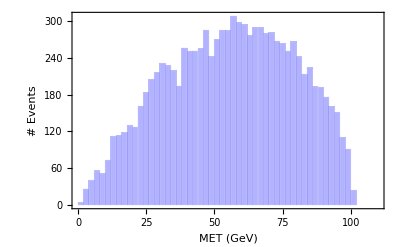

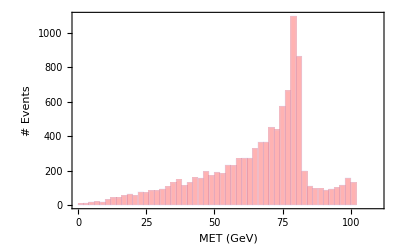

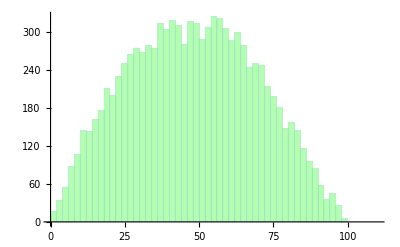

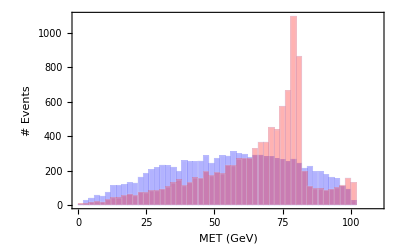

```mathematica
g1=Histogram[ptmissAxPlot , {0,110,2},ChartStyle->{Directive[Blue,Opacity[.3]]},BaseStyle->{FontWeight->"Bold",FontSize->18},Axes->True,AxesOrigin->{0,0},ImageSize->Scaled[.4],Frame->True,FrameLabel->{"MET (GeV)","# Events"}]
g2=Histogram[ptmissGrvPlot, {0,110,2},ChartStyle->{Directive[Red,Opacity[.3]]},BaseStyle->{FontWeight->"Bold",FontSize->18},Axes->True,AxesOrigin->{0,0},ImageSize->Scaled[.4],Frame->True,FrameLabel->{"MET (GeV)","# Events"}]
g3=Histogram[ptmissRPVPlot,{0,110,2},ChartStyle->{Directive[Green,Opacity[.3]]},BaseStyle->{FontWeight->"Bold",FontSize->18},Axes->True,AxesOrigin->{0,0}]
Show[g1,g2]
```

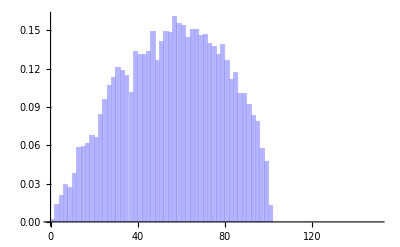

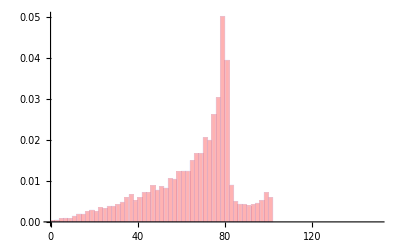

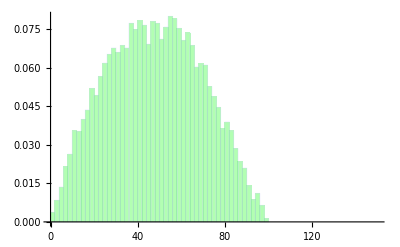

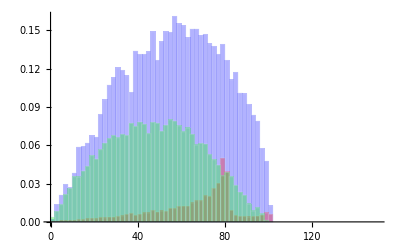

```mathematica
g1=WeightedHistogram[weightListAx->MHTAxPlot , {0,150,2},ChartStyle->{Directive[Blue,Opacity[.3]]},BaseStyle->{FontWeight->"Bold",FontSize->18},Axes->True,AxesOrigin->{0,0}]
g2=WeightedHistogram[weightListGrv->MHTGrvPlot, {0,150,2},ChartStyle->{Directive[Red,Opacity[.3]]},BaseStyle->{FontWeight->"Bold",FontSize->18},Axes->True,AxesOrigin->{0,0}]
g3=WeightedHistogram[weightListRPV->MHTRPVPlot,{0,150,2},ChartStyle->{Directive[Green,Opacity[.3]]},BaseStyle->{FontWeight->"Bold",FontSize->18},Axes->True,AxesOrigin->{0,0}]

Show[g1,g2,g3]
```

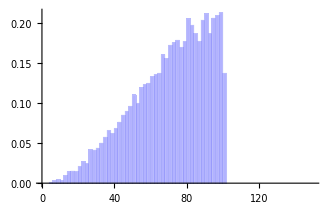

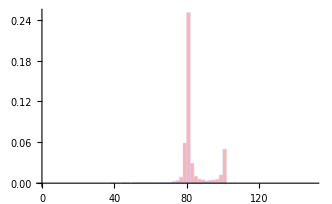

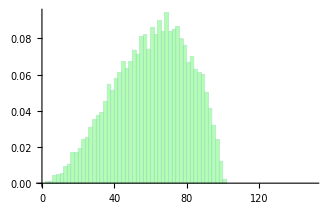

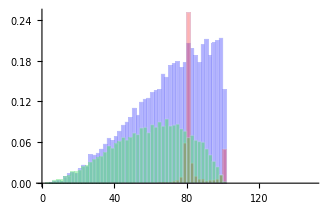

```mathematica
g1=WeightedHistogram[weightListAx->missingEnergyAxPlot , {0,150,2},ChartStyle->{Directive[Blue,Opacity[.3]]},BaseStyle->{FontWeight->"Bold",FontSize->18},Axes->True,AxesOrigin->{0,0}]
g2=WeightedHistogram[weightListGrv->missingEnergyGrvPlot, {0,150,2},ChartStyle->{Directive[Red,Opacity[.3]]},BaseStyle->{FontWeight->"Bold",FontSize->18},Axes->True,AxesOrigin->{0,0}]
g3=WeightedHistogram[weightListRPV->missingEnergyRPVPlot, {0,150,2},ChartStyle->{Directive[Green,Opacity[.3]]},BaseStyle->{FontWeight->"Bold",FontSize->18},Axes->True,AxesOrigin->{0,0}]
Show[g1,g2,g3]
```

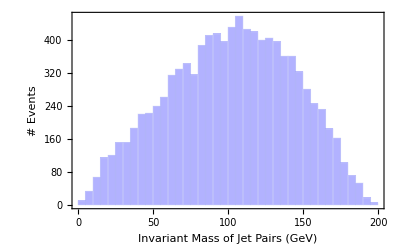

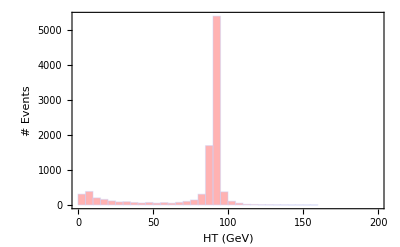

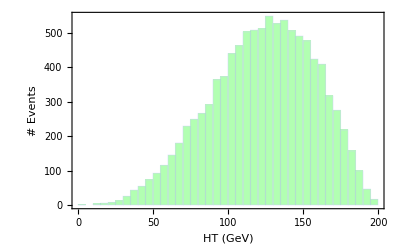

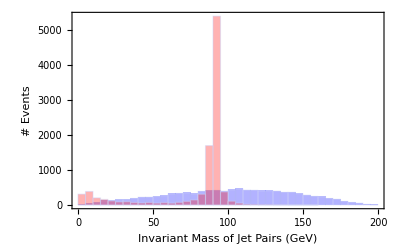

```mathematica
g1=Histogram[JetInvMassAxPlot, {0,200,5},ChartStyle->{Directive[Blue,Opacity[.3]]},BaseStyle->{FontWeight->"Bold",FontSize->18},Axes->True,AxesOrigin->{0,0},ImageSize->Scaled[.4],Frame->True,FrameLabel->{"Invariant Mass of Jet Pairs (GeV)","# Events"}]
g2=Histogram[JetInvMassGrvPlot, {0,200,5},ChartStyle->{Directive[Red,Opacity[.3]]},BaseStyle->{FontWeight->"Bold",FontSize->18},Axes->True,AxesOrigin->{0,0},ImageSize->Scaled[.4],Frame->True,FrameLabel->{"HT (GeV)","# Events"}]
g3=Histogram[JetInvMassRPVPlot, {0,200,5},ChartStyle->{Directive[Green,Opacity[.3]]},BaseStyle->{FontWeight->"Bold",FontSize->18},Axes->True,AxesOrigin->{0,0},ImageSize->Scaled[.4],Frame->True,FrameLabel->{"HT (GeV)","# Events"}]
Show[g1,g2]
```

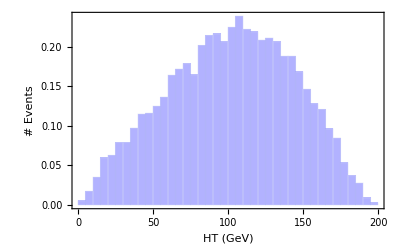

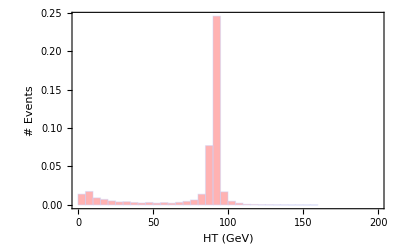

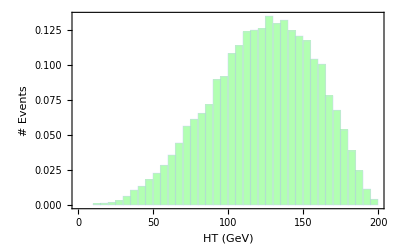

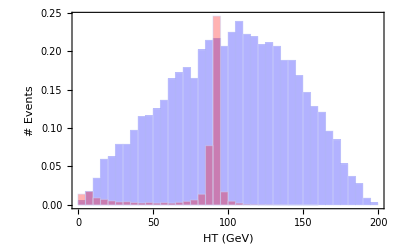

```mathematica
g1=WeightedHistogram[weightListAx->JetInvMassAxPlot, {0,200,5},ChartStyle->{Directive[Blue,Opacity[.3]]},BaseStyle->{FontWeight->"Bold",FontSize->18},Axes->True,AxesOrigin->{0,0},ImageSize->Scaled[.4],Frame->True,FrameLabel->{"HT (GeV)","# Events"}]
g2=WeightedHistogram[weightListGrv->JetInvMassGrvPlot, {0,200,5},ChartStyle->{Directive[Red,Opacity[.3]]},BaseStyle->{FontWeight->"Bold",FontSize->18},Axes->True,AxesOrigin->{0,0},ImageSize->Scaled[.4],Frame->True,FrameLabel->{"HT (GeV)","# Events"}]
g3=WeightedHistogram[weightListRPV->JetInvMassRPVPlot, {0,200,5},ChartStyle->{Directive[Green,Opacity[.3]]},BaseStyle->{FontWeight->"Bold",FontSize->18},Axes->True,AxesOrigin->{0,0},ImageSize->Scaled[.4],Frame->True,FrameLabel->{"HT (GeV)","# Events"}]

Show[g1,g2]
```

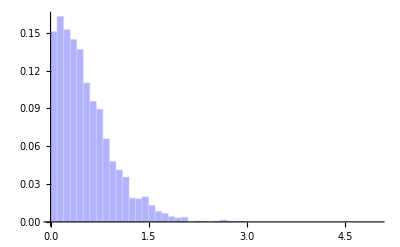

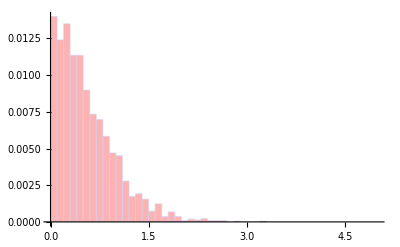

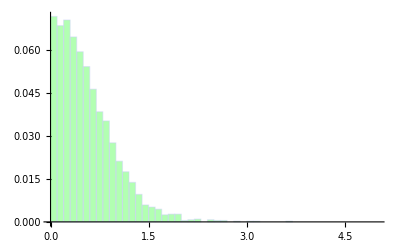

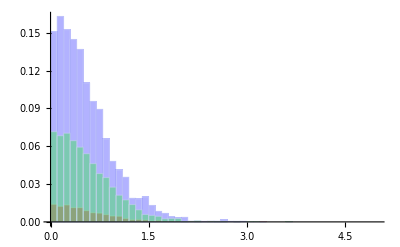

```mathematica
g1=WeightedHistogram[weightListAx->etaHardestAxPlot, {0,5,0.1},ChartStyle->{Directive[Blue,Opacity[.3]]},BaseStyle->{FontWeight->"Bold",FontSize->18},Axes->True,AxesOrigin->{0,0}]
g2=WeightedHistogram[weightListGrv->etaHardestGrvPlot, {0,5,0.1},ChartStyle->{Directive[Red,Opacity[.3]]},BaseStyle->{FontWeight->"Bold",FontSize->18},Axes->True,AxesOrigin->{0,0}]
g3=WeightedHistogram[weightListRPV->etaHardestRPVPlot, {0,5,0.1},ChartStyle->{Directive[Green,Opacity[.3]]},BaseStyle->{FontWeight->"Bold",FontSize->18},Axes->True,AxesOrigin->{0,0}]

Show[g1,g2,g3]
```

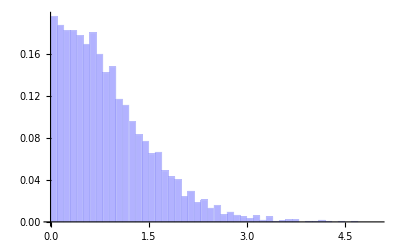

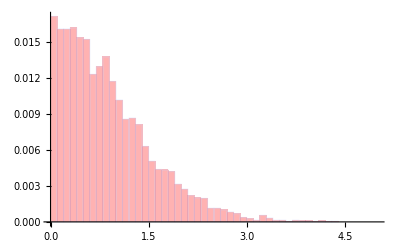

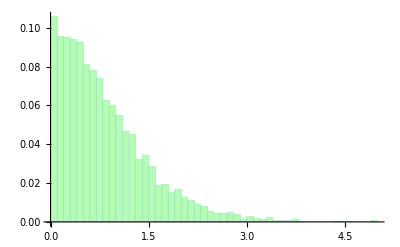

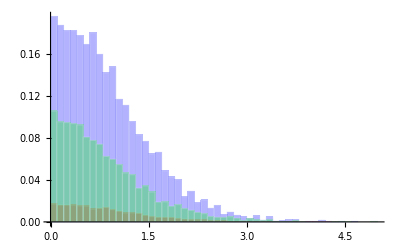

```mathematica
g1=WeightedHistogram[weightListAx->etaSoftestAxPlot, {0,5,0.1},ChartStyle->{Directive[Blue,Opacity[.3]]},BaseStyle->{FontWeight->"Bold",FontSize->18},Axes->True,AxesOrigin->{0,0}]
g2=WeightedHistogram[weightListGrv->etaSoftestGrvPlot,{0,5,0.1},ChartStyle->{Directive[Red,Opacity[.3]]},BaseStyle->{FontWeight->"Bold",FontSize->18},Axes->True,AxesOrigin->{0,0}]
g3=WeightedHistogram[weightListRPV->etaSoftestRPVPlot,{0,5,0.1},ChartStyle->{Directive[Green,Opacity[.3]]},BaseStyle->{FontWeight->"Bold",FontSize->18},Axes->True,AxesOrigin->{0,0}]
Show[g1,g2,g3]
```

LessEqual::nord: Invalid comparison with 0.  + 2.05462\ ⅈ attempted.

Less::nord: Invalid comparison with 0.  + 2.05462\ ⅈ attempted.

LessEqual::nord: Invalid comparison with 0.  + 2.05462\ ⅈ attempted.

Less::nord: Invalid comparison with 0.  + 2.05462\ ⅈ attempted.

LessEqual::nord: Invalid comparison with 0.  + 0.665032\ ⅈ attempted.

General::stop: Further output of LessEqual :: nord will be suppressed during this calculation.

Less::nord: Invalid comparison with 0.  + 0.665032\ ⅈ attempted.

General::stop: Further output of Less :: nord will be suppressed during this calculation.

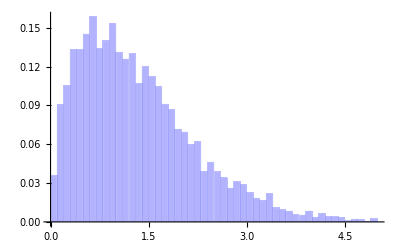

LessEqual::nord: Invalid comparison with 0.  + 0.332091\ ⅈ attempted.

Less::nord: Invalid comparison with 0.  + 0.332091\ ⅈ attempted.

LessEqual::nord: Invalid comparison with 0.  + 0.332091\ ⅈ attempted.

Less::nord: Invalid comparison with 0.  + 0.332091\ ⅈ attempted.

LessEqual::nord: Invalid comparison with 0.  + 1.0706\ ⅈ attempted.

General::stop: Further output of LessEqual :: nord will be suppressed during this calculation.

Less::nord: Invalid comparison with 0.  + 1.0706\ ⅈ attempted.

General::stop: Further output of Less :: nord will be suppressed during this calculation.

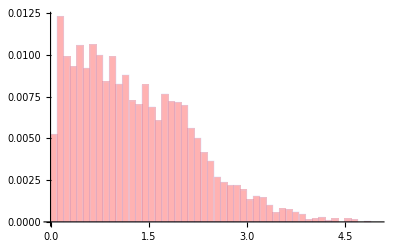

LessEqual::nord: Invalid comparison with 0.  + 0.368025\ ⅈ attempted.

Less::nord: Invalid comparison with 0.  + 0.368025\ ⅈ attempted.

LessEqual::nord: Invalid comparison with 0.  + 0.368025\ ⅈ attempted.

Less::nord: Invalid comparison with 0.  + 0.368025\ ⅈ attempted.

LessEqual::nord: Invalid comparison with 0.  + 0.846345\ ⅈ attempted.

General::stop: Further output of LessEqual :: nord will be suppressed during this calculation.

Less::nord: Invalid comparison with 0.  + 0.846345\ ⅈ attempted.

General::stop: Further output of Less :: nord will be suppressed during this calculation.

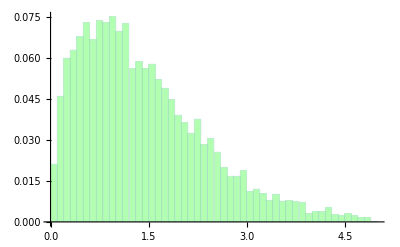

```mathematica
g1=WeightedHistogram[weightListAx->drjjAxPlot, {0,5,0.1},ChartStyle->{Directive[Blue,Opacity[.3]]},BaseStyle->{FontWeight->"Bold",FontSize->18},Axes->True,AxesOrigin->{0,0}]
g2=WeightedHistogram[weightListGrv->drjjGrvPlot,{0,5,0.1},ChartStyle->{Directive[Red,Opacity[.3]]},BaseStyle->{FontWeight->"Bold",FontSize->18},Axes->True,AxesOrigin->{0,0}]
g3=WeightedHistogram[weightListRPV->drjjRPVPlot,{0,5,0.1},ChartStyle->{Directive[Green,Opacity[.3]]},BaseStyle->{FontWeight->"Bold",FontSize->18},Axes->True,AxesOrigin->{0,0}]
```